```mathematica
(* redefining Wald CI for convenience *) 
interWald[jj_, nn_,confLvl_]:=With[{t025=Quantile[NormalDistribution[],1 - (1-confLvl)/2]},Interval[Max[0,#]&/@{jj/nn -t025  √(jj/nn (1-jj/nn)/nn),jj/nn +t025  √(jj/nn (1-jj/nn)/nn)}]];

(* redefining Wilson CI for convenience *) 
interWilson[jj_, nn_,confLvl_]:=With[{t025=Quantile[NormalDistribution[],1 - (1-confLvl)/2]}, Interval[{1/(1+t025^2/nn)(jj/nn+1/(2 nn) t025^2-t025 √((jj/nn (1-jj/nn))/nn+t025^2/(4 nn^2))),1/(1+t025^2/nn)(jj/nn+1/(2 nn) t025^2+t025 √((jj/nn (1-jj/nn))/nn+t025^2/(4 nn^2)))}]];
```

```mathematica
Clear[monFilenames,  allMonFilenames, detFilenames, allDetFilenames, iterationDirName, countFromFiles]

(*** SESSION-SPECIFIC HACKS ***) 

(* hardcoded paths *) 
(*dataDirPathSesh4 = "~/Dropbox/upenn/research/aa/monitoring_data/data/Session_4_Sonar_Nocontroller_8Aug2019/";
dataDirPathSesh5 = "~/Dropbox/upenn/research/aa/monitoring_data/data/Session_5_Sonar_Nocontroller_9Sept_2019/";
dataDirPathSesh6 = "~/Dropbox/upenn/research/aa/monitoring_data/data/Session_6_Sonar_Nocontroller_23Sept_2019/";*)

(* session number -> data directory for it *) 
dataDirPathForSeshNum[seshNum_]:= Switch[seshNum, All,"/home/ivan/Dropbox/upenn/research/aa/monitoring_data/data/", 4, "~/Dropbox/upenn/research/aa/monitoring_data/data/Session_4_Sonar_Nocontroller_8Aug2019/", 5,"~/Dropbox/upenn/research/aa/monitoring_data/data/Session_5_Sonar_Nocontroller_9Sept_2019/",6,"~/Dropbox/upenn/research/aa/monitoring_data/data/Session_6_Sonar_Nocontroller_23Sept_2019/",7, "~/Dropbox/upenn/research/aa/monitoring_data/data/Session_7_Sonar_Nocontroller_3Oct_2019/",
 _ , Throw[StringJoin["Unknown session number: ", ToString[seshNum]] ]];

(* a hack to determine different spellings of Iteration_1 or Iteration1, given session info *)
iterationDirName[seshNum_]:= If[seshNum == 4, "Iteration_", "Iteration"];

(* a hack to determine complete pairlists for each session; the triples are (seshnum, iternum, detnum) *)
fullTripleList[seshNums_]:= Flatten[Switch[#, 4,(* for session 4 *) Join[{4}, #]& /@Flatten[Outer[List, Range[1,5], Range[1,5]], 1], 5,(* for session 5 *)Join[{5}, #]& /@ Flatten[Outer[List, Range[1,5],{1}], 1],6,(* for session 6 *)Join[{6}, #]& /@ Flatten[Outer[List, Range[1,24],{1}], 1],
7,(* for session 7 *)Join[{7}, #]& /@ Flatten[Outer[List, Range[1,39],{1}], 1],
 _, {}]& /@ seshNums, 1];

fullTripleListNoRedun[seshNums_]:= Flatten[Switch[#, 4,(* for session 4 *) Join[{4}, #]& /@Flatten[Outer[List, Range[1,5],{1}], 1], 5,(* for session 5 *)Join[{5}, #]& /@ Flatten[Outer[List, Range[1,5],{1}], 1],6,(* for session 6 *)Join[{6}, #]& /@ Flatten[Outer[List, Range[1,24],{1}], 1],
7,(* for session 7 *)Join[{7}, #]& /@ Flatten[Outer[List, Range[1,39],{1}], 1], _, {}]& /@ seshNums, 1];


(*** FILE MANIPULATIONS ***)

monFilenames[idtriplelist_, winSize_] := StringJoin[dataDirPathForSeshNum@#[[1]],iterationDirName[#[[1]]], ToString[#[[2]]], "/mon", ToString[#[[3]]], "_",ToString[winSize], "/iter", ToString[#[[2]]], "_mondet", ToString[#[[3]]], "_",ToString@winSize, "_estrates.txt"] & /@idtriplelist;

detFilenames[idtriplelist_, dummyArg_:Null] := StringJoin[dataDirPathForSeshNum@#[[1]],iterationDirName[#[[1]]], ToString[#[[2]]], "/det", ToString[#[[3]]], "/iter", ToString[#[[2]]], "_both_det_estrates.txt"] & /@idtriplelist;

allMonFilenames[seshNums_, winSize_] := Flatten[monFilenames[fullTripleList[{#}], winSize] & /@ seshNums];

allDetFilenames[seshNums_, dummyArg_:Null] := Flatten[detFilenames[fullTripleList[{#}]] & /@ seshNums];


(* add up a given field's values over filenames *) 
countFromFiles[fieldName_, filenames_] := Plus@@(*list of frame numbers from each*)(getValueFromListOfPairs[#,fieldName]& /@ (*list of all stat dicts*) (nameValuePairsFromFile/@filenames(*list of filenames*)))
```

```mathematica
(* various counts from mons, for sanity *) 
allMonH1ct = countFromFiles[ "h1count",allMonFilenames[{4,5,6,7},10]]
allMonFNct = countFromFiles[ "FNcount",allMonFilenames[{4,5,6,7},10]]
allDetH0ct =countFromFiles[ "h0count",allDetFilenames[{4,5,6,7}]]
allDetFPct =countFromFiles[ "FPcount",allDetFilenames[{4,5,6,7}]]
```

2041

1357

3310

351

```mathematica
(* PREDICTIONS basics *) 
Clear[predFNR, chart95conf,subsetCt,allSubsetCt]

predFNR[detFPR_, monWin_, pDetNCH0_:0(* for this context *)] := 1 - (1-detFPR)(1 - detFPR - pDetNCH0)^(monWin-1);

chart95conf[maxSampleSize_] := ListLinePlot[Inner[List, Range[0,maxSampleSize],Table[0.95, maxSampleSize+1], List], PlotStyle->{Red, Dotted}];(*ListLinePlot[Table[0.95, 25], PlotStyle->{Red, Dotted}];*)

chartHorLine[yLineValue_, maxSampleSize_, color_:Green] := ListLinePlot[Inner[List, Range[0,maxSampleSize],Table[yLineValue, maxSampleSize+1], List], PlotStyle->{color, Dotted}];

chartVertLine[xLineValue_, maxY_ ,minY_:0, color_:Green] := ListLinePlot[Inner[List, Table[xLineValue, maxY+1], Range[minY,maxY],List], PlotStyle->{color, Dotted}];

(* number of subsets excluding the empty one *) 
subsetCt[set_] := 2^(Length@set)-1;
subsetCtOfSize[set_, subsetSize_]:= Binomial[Length@set, subsetSize];
allSubsetCt = subsetCt@fullTripleList[{4,5}];
```

```mathematica
(*** DATA ANALYSIS ***)
Clear[pairingPredMonFNR, oneIntervalTestGeneral, generateBinarySampleNonRepl,tallyUpBinarySample, generateCIRSOutcomesGeneral]

(** Pairings **)
(* returns basic pairing between interval and prediction point: (interval from data, prediction/gt) *)

(* TODO: factor out monitor win size as a parameter to something else *) 

(* for predicted monitor FNR *)
pairingPredMonFNR[tripleIdList_,monWinSize_, intervalType_: interWald, confidence_:0.95] := {(* interval *) intervalType[countFromFiles[ "FNcount",monFilenames[tripleIdList, monWinSize ]], countFromFiles[ "h1count",monFilenames[tripleIdList, monWinSize ]], confidence], (* prediction *) predFNR[countFromFiles[ "FPcount",detFilenames@tripleIdList]/countFromFiles[ "h0count",detFilenames@tripleIdList], monWinSize]};

(* for GT monitor FNR *)
pairingGtMonFNR[tripleIdList_,monWinSize_, intervalType_: interWald, confidence_:0.95] := {(* interval *) intervalType[countFromFiles[ "FNcount",monFilenames[tripleIdList, monWinSize ]], countFromFiles[ "h1count",monFilenames[tripleIdList, monWinSize ]], confidence], (* prediction *) predFNR[0.1, monWinSize]};


(* for detector FPR prediction -- both are from data *) 
pairingPredDetFPR[tripleIdList_,monWinSize_:-1(*not used*), intervalType_: interWald, confidence_:0.95] := With[{fps =countFromFiles[ "FPcount",detFilenames[tripleIdList ]], hos = countFromFiles[ "h0count",detFilenames[tripleIdList ]]} ,{(* interval *) intervalType[fps,hos, confidence], (* prediction *) fps/hos}];

(* for detector GT FPR *) 
pairingGtDetFPR[tripleIdList_,monWinSize_:-1(*not used*), intervalType_: interWald, confidence_:0.95] := {(* interval *) intervalType[countFromFiles[ "FPcount",detFilenames[tripleIdList ]], countFromFiles[ "h0count",detFilenames[tripleIdList ]], confidence], (* ground truth *) 0.1};

(* for detector FNR prediction -- both are from data *) 
pairingPredDetFNR[tripleIdList_,monWinSize_:-1(*not used*), intervalType_: interWald, confidence_:0.95] := With[{fns =countFromFiles[ "FNcount",detFilenames[tripleIdList ]], h1s = countFromFiles[ "h1count",detFilenames[tripleIdList ]]} ,{(* interval *) intervalType[fns,h1s, confidence], (* prediction *) fns/h1s}];

(* for detector GT FNR *) 
pairingGtDetFNR[tripleIdList_,monWinSize_:-1(*not used*), intervalType_: interWald, confidence_:0.95] := {(* interval *) intervalType[countFromFiles[ "FNcount",detFilenames[tripleIdList ]], countFromFiles[ "h1count",detFilenames[tripleIdList ]], confidence], (* ground truth *) 0.1};


(* generates a true/false response for intervals containing things in pairs, for a particular pairing function *) 
oneIntervalTestGeneral[pairingFn_,tripleIdList_,monWinSize_,  intervalType_:interWald, confidence_:0.95 ] := 
With[{testPair = pairingFn[tripleIdList,monWinSize,intervalType, confidence]}, IntervalMemberQ[testPair[[1]], testPair[[2]]]];

(* just returns the pair, mostly for visualization *) 
oneIntervalTestRetPair[pairingFn_,tripleIdList_,monWinSize_,  intervalType_:interWald, confidence_:0.95 ] := 
pairingFn[tripleIdList,monWinSize,intervalType, confidence];


(*** IMPLEMENTATIONS OF SAMPLING ***) 

(** Option 1a: Randomized NON-REPLACEMENT sampling across all subsets **) 
Clear[generateBinarySampleNonRepl, tallyUpBinarySample,generateCIRSOutcomesGeneral];

(* returns a list of pairs {subset size used, whether CI contains the prediciton}. Can do tripling if needed *) 
generateBinarySampleNonRepl[pairingFn_, seshNums_, totalSampleCt_, monWinSize_, intervalType_:interWald, confidence_:0.95, testFn_:oneIntervalTestGeneral]:= With[{tripleList =fullTripleList[seshNums] },({#[[1]],testFn[pairingFn, #[[2]],monWinSize, intervalType, confidence]}&/@( Flatten[{Length@#, #} &/@(* list of lists of subsets of possible sets of pairs for tests.
aka: {   {subsetsize, triplelist}, {subsetsize, triplelist, ...}   } *) Subsets[tripleList,{1, Length@tripleList},{#}] &/@ (* getting random subsets *)  RandomInteger[{1,(*all subsets *)subsetCt[tripleList]
},totalSampleCt],1]))];

(* Represents trues and falses as counts, in triples of {subsetsize, # of trues at that size, # of falses at that size}.
Takes in a list of pairs {subset size, true/false} *)
tallyUpBinarySample[sample_, maxSubsetSize_]:= With[ {trueCt= Count[sample, {#, True}], falseCt= Count[sample, {#, False}]} , {#,trueCt, falseCt}]& /@  Range[1,maxSubsetSize];

(* Evaluation of CI via random NON-REPLACEMENT sampling  across all subsets, producing outcome pairs {subset size, accuracy w/uncert based on wilson CIs}, by converting tallied triples to ratios and stdev *) 
generateCIRSOutcomesGeneral[pairingFn_, seshNums_, sampleCt_, monWinSize_, intervalTypeForEstim_:interWald, intervalTypeForEval_:interWald,confidence_:0.95, testFn_:oneIntervalTestGeneral]:={(*subset size*) #[[1]], (*ratio of successes to total *) With[{est = #[[2]]/(#[[2]]+#[[3]]), int = intervalTypeForEval[#[[2]],#[[2]]+#[[3]], 0.95]},Around[(*estimated accuracy*)est,(* converting wilson interval to uncertainty bounds*) {Min@int-est, Max@int-est}]] }&/@ (* getting tallied sample data and filtering it*)Select[tallyUpBinarySample[generateBinarySampleNonRepl[pairingFn, seshNums, sampleCt,monWinSize, intervalTypeForEstim,confidence, testFn], Length@fullTripleList@seshNums], #[[2]] >0 ∨ #[[3]]>0 # &];

(** Option 1b: Fixed subsets, non-replacement **) 
Clear[generateSuccessCtsPerSubsetSize,  generateSuccessCtsPerSubsetSizeForCharting, generateCIOutcomesPerSubsetSize];

(* sample success counts fixed per subset size;
returns a list of (# of samples correct) *) 
generateSuccessCtsPerSubsetSize[pairingFn_, triplingFn_, seshNums_, monWinSize_, samplesPerSubsetSize_, intervalType_:interWald, confidence_:0.95,testFn_:oneIntervalTestGeneral]  := With[{subsetsCt = #},
(* count truths *)Count[ (* apply test function, get T/F *) testFn[pairingFn, #, monWinSize, intervalType, confidence]&/@ (* all possible sets of pairs for tests *) Subsets[triplingFn@seshNums, {subsetsCt},{#}] &/@ (* getting samplesPerSubsetSize random subsets *)  RandomInteger[{1,(*counting subsets *)subsetCtOfSize[triplingFn@seshNums, subsetsCt]
},samplesPerSubsetSize], {True}]
]& /@ (* iterating through subset sizes *) Range[1, Length@triplingFn@seshNums];

(* adds lengths to each count and divides it by the length *)
generateSuccessCtsPerSubsetSizeForCharting[pairingFn_, triplingFn_, seshNums_, monWinSize_, samplesPerSubsetSize_, intervalType_:interWald, confidence_:0.95,testFn_:oneIntervalTestGeneral] := With[{successCts = generateSuccessCtsPerSubsetSize[pairingFn,triplingFn, seshNums, monWinSize, samplesPerSubsetSize, intervalType, confidence,testFn]},Inner[List,Range[1,Length@successCts], successCts/samplesPerSubsetSize, List]];

(* generates confidence intervals out of the above success counts *) 
generateCIOutcomesPerSubsetSize[pairingFn_,triplingFn_, seshNums_, monWinSize_, sampleCtPerSubsetSize_,intervalTypeForEstim_:interWald, intervalTypeForEval_:interWald,confidence_:0.95, testFn_:oneIntervalTestGeneral]:= Inner[List, Range[1,Length@triplingFn@seshNums], #, List]& @(With[{est = #/ sampleCtPerSubsetSize, int = intervalTypeForEval[#, sampleCtPerSubsetSize, confidence ]}, Around[(*estimated accuracy*)est,(* converting interval to uncertainty bounds for charts*) {Min@int-est, Max@int-est}]] &/@generateSuccessCtsPerSubsetSize[pairingFn,triplingFn, seshNums, monWinSize, sampleCtPerSubsetSize, intervalTypeForEstim,confidence, testFn] );

(* -- returns a triple and whether the test succeeded for it *) 
generateSuccessOutcomeWithTripleset[pairingFn_, triplingFn_, seshNums_, monWinSize_, samplesPerSubsetSize_, intervalType_:interWald, confidence_:0.95,testFn_:oneIntervalTestGeneral]  := Flatten[ With[{subsetsCt = #},
(* apply test function, get T/F *)  {#, testFn[pairingFn, #, monWinSize, intervalType, confidence]} &/@ (* all possible sets of pairs for tests *) Subsets[triplingFn@seshNums, {subsetsCt},{#}] &/@ (* getting samplesPerSubsetSize random subsets *)  RandomInteger[{1,(*counting subsets *)subsetCtOfSize[triplingFn@seshNums, subsetsCt]
},samplesPerSubsetSize]
]& /@ (* iterating through subset sizes *) Range[1, Length@triplingFn@seshNums], 2];

(* tallies up the amount of information in the list of (tripleset, result) while preserving the result *)
tallyInfoInTriplesets[tripleSetList_, infoString_, filenamesFn_, filenamesFnArg_:Null]:= {countFromFiles[infoString, filenamesFn[#[[1]],filenamesFnArg]], #[[2]]} & /@ tripleSetList;

(** Option 2: Randomized (with REPLACEMENT) sampling across subsets **) 
Clear[getRandomTriple, getRandomTripleListWithRepl, generateTestedSampleRepl, generateReplSamplesForCharting];

(* get a random trace *) 
getRandomTriple[seshNums_] := With[{triples = fullTripleList[seshNums]},triples[[RandomInteger[{1,Length@triples}]]]];

(* get random subset of traces with replacement *)
getRandomTripleListWithRepl[seshNums_, size_]:= Table[getRandomTriple[seshNums], size];

(* generates a number of true attempts out of sampleCt *)
generateTestedSampleRepl[pairingFn_, seshNums_, traceCtInSample_, sampleCt_, monWinSize_, intervalType_:interWald, confidence_:0.95, testFn_:oneIntervalTestGeneral]:= Count[True]@(testFn[pairingFn, #,monWinSize, intervalType, confidence]&/@ (* get a triple at a time *)
Table[getRandomTripleListWithRepl[seshNums, traceCtInSample], sampleCt]);

(* generate samples across all trace counts *)
generateReplSamplesForCharting[pairingFn_, seshNums_,  maxTraceCtInSample_, sampleCt_, monWinSize_, intervalTypeForEstim_:interWald,intervalTypeForEval_:interWald, confidence_:0.95, testFn_:oneIntervalTestGeneral]:= 
{(*size of sample*) #[[1]], (*ratio of successes to total *) With[{est = #[[2]]/sampleCt, int = intervalTypeForEval[#[[2]],sampleCt, confidence]},Around[(*estimated accuracy*)est,(* converting wilson interval to uncertainty bounds*) {Min@int-est, Max@int-est}]] }&/@ 
(* list of (trace count, number of successes out of sampleCt) *) 
({#, generateTestedSampleRepl[pairingFn,seshNums,(*trace ct in sample*)#, sampleCt, 10]}&/@Range[1,  maxTraceCtInSample] );

(* getting tallied sample data and filtering it*)(*Select[tallyUpBinarySample[generateBinarySampleNonRepl[pairingFn, seshNums, sampleCt,monWinSize, intervalTypeForEstim,confidence, testFn], Length@fullTripleList@seshNums], #[[2]] >0 ∨ #[[3]]>0 # &]*)


(** Option 3: splitting into completely independent, disjoint subsets and testing each. Data-hungry **)

(* generates a partition of triples and tries each as a binary test *)
generatePartitionSample[pairingFn_, seshNums_, partitionSize_, monWinSize_, intervalType_:interWald, confidence_:0.95, testFn_:oneIntervalTestGeneral]:= With[{tripleList =fullTripleList[seshNums] },testFn[pairingFn, #,monWinSize, intervalType, confidence] &/@ Partition[tripleList,partitionSize]];

generatePartitionOutcomesForCharting[pairingFn_, seshNums_, maxPartitionSize_, monWinSize_, intervalTypeForEstim_:interWald, intervalTypeForEval_:interWald, confidence_:0.95, testFn_:oneIntervalTestGeneral] :=
{(*size of partition*) #[[1]], (*ratio of successes to total *) With[{est = #[[3]]/#[[2]], int = intervalTypeForEval[#[[3]],#[[2]], confidence]},Around[(*estimated accuracy*)est,(* converting wilson interval to uncertainty bounds*) {Min@int-est, Max@int-est}]] }&/@ 
(* list of (partition size, number of successes) *) 
(With[{binarySample = generatePartitionSample[pairingFn,   seshNums, #, monWinSize]}, {#, Length@binarySample, Count[binarySample, True]} ]&/@  Range[1, maxPartitionSize]  );

(** Option 4, THREE-WAY COMPARISON: CI, Prediction for MonFNR, and GT for MonFNR 
it is a success if we either hit the interval or both we and GT miss it 
**) 

(* returns a triple {CI interval from data, predicted FNR, GT FNR} *)
threewayPairingMonFNRCIPredGt[tripleIdList_,monWinSize_, intervalType_: interWald, confidence_:0.95] := {(* interval *) intervalType[countFromFiles[ "FNcount",monFilenames[tripleIdList, monWinSize]], countFromFiles[ "h1count",monFilenames[tripleIdList,monWinSize]], confidence], (* prediction *) predFNR[countFromFiles[ "FPcount",detFilenames[tripleIdList]]/countFromFiles[ "h0count",detFilenames[tripleIdList]],monWinSize], (* GT of FNR *) predFNR[0.1, monWinSize]};

(* returns false only if we missed the CI but the GT hit the CI *)
oneIntervalThreewayTest[threewayPairingFn_,tripleIdList_, monWinSize_,  intervalType_:interWald, confidence_:0.95 ] := 
With[{(*{CI,pred,GT}*) testTriple = threewayPairingFn[tripleIdList,monWinSize, intervalType, confidence]}, IntervalMemberQ[testTriple[[1]], testTriple[[2]]]∨¬IntervalMemberQ[testTriple[[1]], testTriple[[3]]] ];
```

```mathematica
(*** ACTUAL COMPUTATIONS ***)

(** Option 1b: fixed samples per subsets **) 

(* old, session 4: get 100 lists of 100 samples  *) 
Table[generateSuccessCtsPerSubsetSize[pairingPredMonFNR, 100, interWilson], 100]
```

```mathematica
reslists100 = ;
```

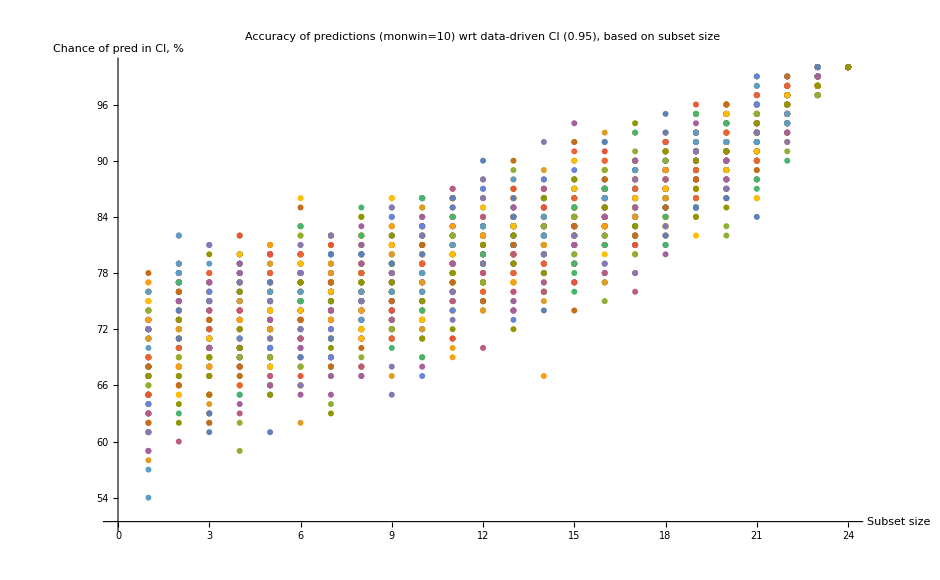

```mathematica
ListPlot[Inner[List, Range[1,24], #, List]& /@ reslists100, AxesLabel->{"Subset size", "Chance of pred in CI, %"}, PlotLabel->"Accuracy of predictions (monwin=10) wrt data-driven CI (0.95), based on subset size"]
```

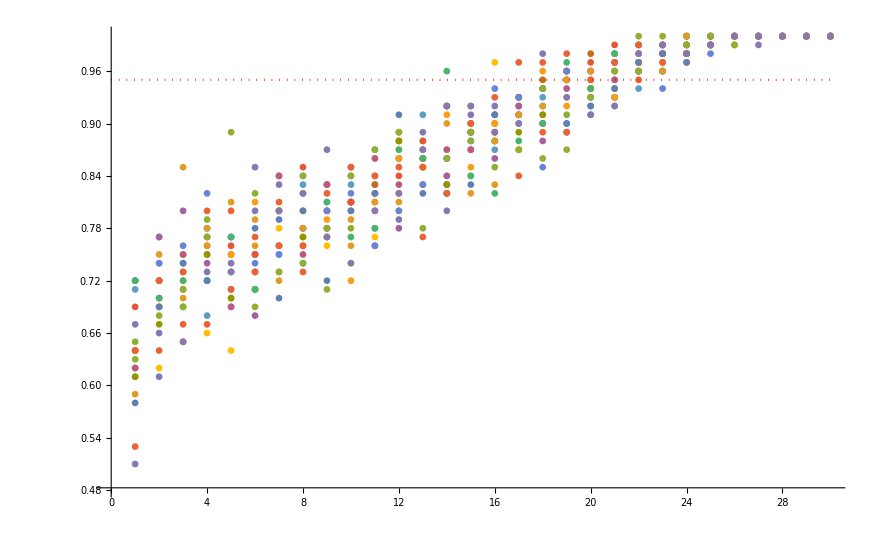
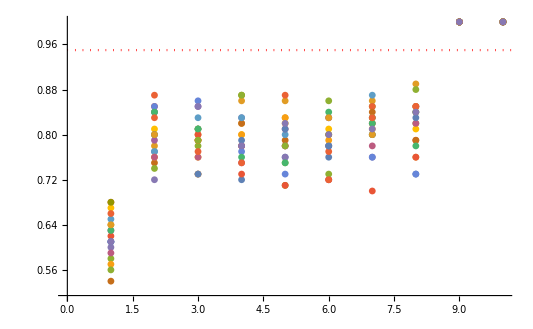
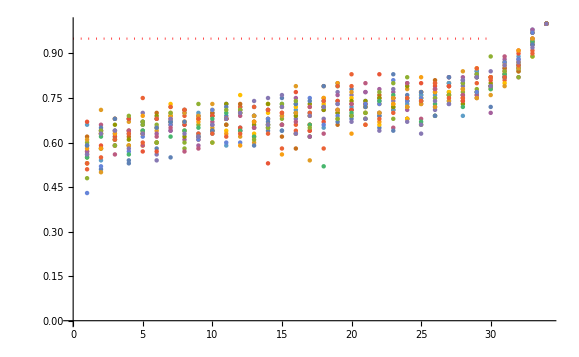
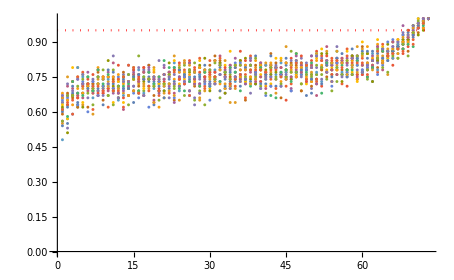
```mathematica
(* same as above but for sessions 4 and 5 *) 
Show[ListPlot@Table[generateSuccessCtsPerSubsetSizeForCharting[pairingPredMonFNR, {4,5}, (*monwin size, ignored in this case*) 10, (* attempts per dot *) 100],(* number of series *) 20],chart95conf[30]] 
-Graphics-

(* for non-redundant subsets *) 
Show[ListPlot@Table[generateSuccessCtsPerSubsetSizeForCharting[pairingPredMonFNR,fullTripleListNoRedun, {4,5}, (*monwin size, ignored in this case*) 10, (* attempts per dot *)100],(* number of series *) 20],chart95conf[30]] 
-Graphics-

(* same for session 6 included *) 
Show[ListPlot@Table[generateSuccessCtsPerSubsetSizeForCharting[pairingPredMonFNR,fullTripleListNoRedun, {4,5,6}, (*monwin size*) 10, (* attempts per dot *)100],(* number of series *) 20],chart95conf[30]] 
-Graphics-

(* same for session 7 included *) 
Show[ListPlot@Table[generateSuccessCtsPerSubsetSizeForCharting[pairingPredMonFNR,fullTripleListNoRedun, {4,5,6,7}, (*monwin size*) 10, (* attempts per dot *)100],(* number of series *) 20],chart95conf[73]] 
-Graphics-
```

```mathematica
(** CIs for Option 1b: INVALID DUE TO DEPENDENCIES **)

(* old, for sesson 4, wilson/wald *) 
 generateCIOutcomesPerSubsetSize[pairingPredMonFNR,1000, interWilson, interWilson]
```

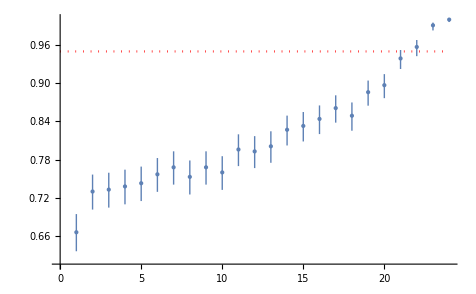

```mathematica
resestimates1000Wilson =;
(* clear dynamic here, despite small samples *) 
Show[ListPlot[resestimates1000Wilson, PlotStyle->PointSize[Large]], chart95conf]
```

```mathematica
generateCIOutcomesPerSubsetSize[pairingPredMonFNR,1000, interWald, interWald]
```

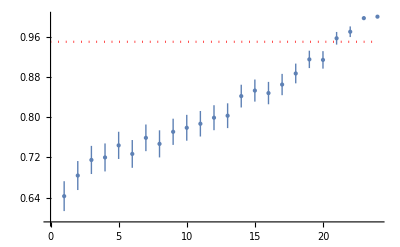

```mathematica
resestimates1000Wald = ;

Show[ListPlot[resestimates1000Wald, PlotStyle->PointSize[Large]], chart95conf]
```

```mathematica
(* larger sample, wilson *)
generateCIOutcomesPerSubsetSize[pairingPredMonFNR,10000, interWilson, interWilson]
```

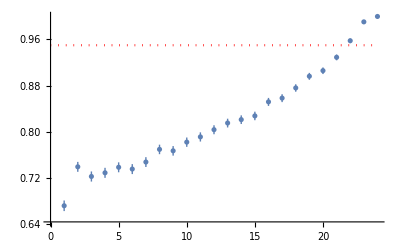

```mathematica
resestimates10000Wilson =;
Show[ListPlot[resestimates10000Wilson], chart95conf]
```

```mathematica
(* larger sample, wald *) 
generateCIOutcomesPerSubsetSize[pairingPredMonFNR,10000, interWald, interWald]
```

```mathematica
resestimates10000Wald = ;
Show[ListPlot[resestimates10000Wald, PlotStyle->PointSize[Medium]], chart95conf]
```

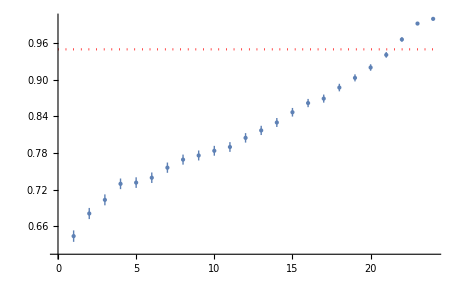

```mathematica
(* now full session 6 included *) 
generateCIOutcomesPerSubsetSize[pairingPredMonFNR,fullTripleList, {4,5,6}, (*monwin size*) 10, (* attempts per subset *)100]
persubsetPredFnrRed100={{1,0.690.090.09},{2,0.660.090.09},{3,0.550.100.10},{4,0.710.090.09},{5,0.730.090.09},{6,0.650.090.09},{7,0.700.090.09},{8,0.560.100.10},{9,0.690.090.09},{10,0.730.090.09},{11,0.670.090.09},{12,0.750.080.08},{13,0.630.090.09},{14,0.680.090.09},{15,0.660.090.09},{16,0.690.090.09},{17,0.630.090.09},{18,0.670.090.09},{19,0.680.090.09},{20,0.690.090.09},{21,0.720.090.09},{22,0.700.090.09},{23,0.670.090.09},{24,0.670.090.09},{25,0.710.090.09},{26,0.730.090.09},{27,0.710.090.09},{28,0.630.090.09},{29,0.690.090.09},{30,0.750.080.08},{31,0.730.090.09},{32,0.680.090.09},{33,0.730.090.09},{34,0.780.080.08},{35,0.700.090.09},{36,0.690.090.09},{37,0.700.090.09},{38,0.750.080.08},{39,0.660.090.09},{40,0.910.060.06},{41,0.750.080.08},{42,0.750.080.08},{43,0.760.080.08},{44,0.760.080.08},{45,0.730.090.09},{46,0.800.080.08},{47,0.840.070.07},{48,0.800.080.08},{49,0.790.080.08},{50,0.860.070.07},{51,0.880.060.06},{52,0.860.070.07},{53,0.950.040.04},{54,1.000000000000000001122}};
```

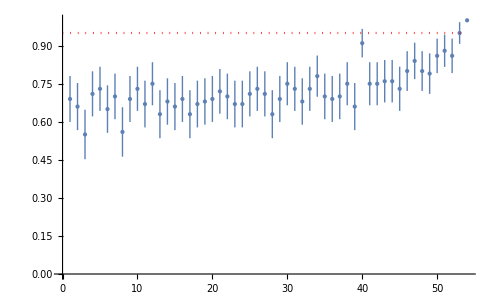

```mathematica
Show[ListPlot[persubsetPredFnrRed100, PlotStyle->PointSize[Medium]], chart95conf[54]]
```

```mathematica
(* session 6 included but no redundancies *) 
generateCIOutcomesPerSubsetSize[pairingPredMonFNR,fullTripleListNoRedun, {4,5,6}, (*monwin size*) 10, (* attempts per subset *)1000]
```

```mathematica
persubsetPredFnr1000={{1,0.5570.0310.031},{2,0.6180.0300.030},{3,0.5830.0310.031},{4,0.6350.0300.030},{5,0.6400.0300.030},{6,0.6370.0300.030},{7,0.6450.0300.030},{8,0.6570.0290.029},{9,0.6750.0290.029},{10,0.6660.0290.029},{11,0.6600.0290.029},{12,0.6690.0290.029},{13,0.6530.0300.030},{14,0.6930.0290.029},{15,0.6820.0290.029},{16,0.7120.0280.028},{17,0.6860.0290.029},{18,0.6930.0290.029},{19,0.7160.0280.028},{20,0.7270.0280.028},{21,0.7160.0280.028},{22,0.7190.0280.028},{23,0.7330.0270.027},{24,0.7410.0270.027},{25,0.7350.0270.027},{26,0.7730.0260.026},{27,0.7770.0260.026},{28,0.7430.0270.027},{29,0.7770.0260.026},{30,0.8080.0240.024},{31,0.8180.0240.024},{32,0.8660.0210.021},{33,0.9580.0120.012},{34,1.000000000000000001122}};
```

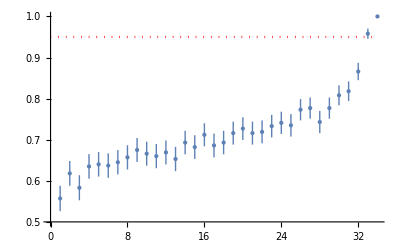

```mathematica
Show[ListPlot[persubsetPredFnr1000, PlotStyle->PointSize[Medium]], chart95conf[34]]
```

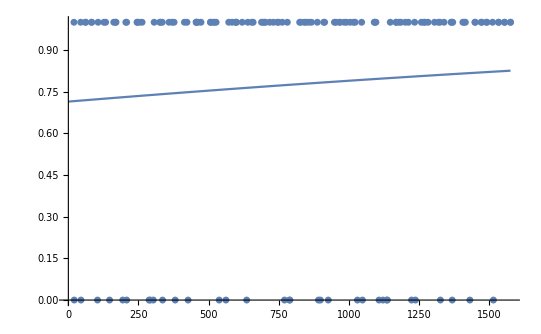
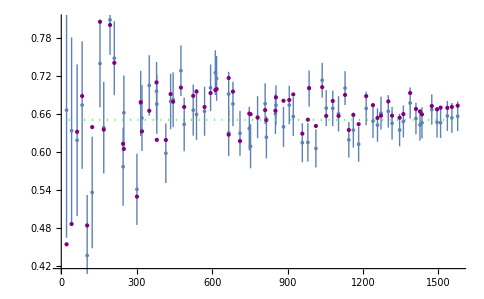
```mathematica
(* plotting with logit mdl -- an experiment for pred FNR *) 
With[{data = (tallyInfoInTriplesets[generateSuccessOutcomeWithTripleSubset[pairingPredMonFNR,fullTripleListNoRedun, {4,5,6,7}, (*monwin size*)10, (* attempts per each subset size *)2], "h1count",monFilenames, 10]) /. {True->1, False->0} }, Show[ListPlot[data], With[{logitmdl =LogitModelFit[data, x,x]},Plot[logitmdl[x],{x, 1, Max@data[[All, 1]] }]]] ]
-Graphics-
(* intervals, estimates, and ground truth *) 
With[{infoIntPointList = tallyInfoInTriplesets[generateSuccessOutcomeWithTripleset[pairingPredMonFNR,fullTripleListNoRedun, {4,5,6,7}, (*monwin size*)10, (* attempts per each subset size *)1, interWald, 0.95, oneIntervalTestRetPair], "h1count",monFilenames, (*monwin again*)10]}, 
With[{interChart =  ListPlot[{#[[1]], #[[2,1]]}&/@infoIntPointList, PlotRange->Full],  
estChart = ListPlot[{#[[1]], #[[2,2]]}&/@infoIntPointList, PlotStyle->{Purple, PointSize[Medium]}], gtChart = chartHorLine[predFNR[0.1, 10], Max@infoIntPointList[[All,1]]]},
Show[interChart, estChart , gtChart]]
]
-Graphics-
```

```mathematica
(* width of interval vs delta between the prediction and the GT *) 
interlenVsErrChart = With[{monWin=10}, With[{infoIntPointList = tallyInfoInTriplesets[generateSuccessOutcomeWithTripleset[pairingPredMonFNR,fullTripleListNoRedun, {4,5,6,7}, (*monwin size*)monWin, (* attempts per each subset size *)2, interWald, 0.95, oneIntervalTestRetPair], "h1count",monFilenames, (*monwin again*)monWin]}, 
With[{interChart =  ListPlot[{#[[1]], (*interval length*)Max@#[[2,1]]-Min@#[[2,1]]}&/@infoIntPointList, PlotRange->Full,PlotStyle->{Lighter@Blue}(*,PlotLegends->Placed[{"Absolute error of the confidence interval's middle"}, Below]*)],  
estChart = ListPlot[{#[[1]],(*delta between prediction and gt*)Abs[#[[2,2]] - predFNR[0.1, monWin]] }&/@infoIntPointList, PlotStyle->{Darker@Magenta, PointSize[Medium]}(*,PlotLegends->Placed[{"Absolute error of our estimate"}, Below]*)]}, 
Show[interChart, estChart ]
]]]
```

$Aborted

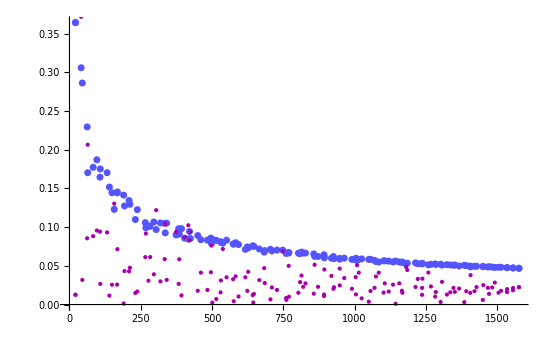

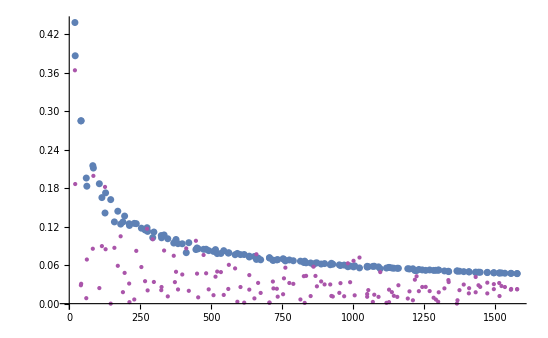

```mathematica
(* same as above but only the interval length *) 
interlenChart = With[{monWin=10}, With[{infoIntPointList = tallyInfoInTriplesets[generateSuccessOutcomeWithTripleset[pairingPredMonFNR,fullTripleListNoRedun, {4,5,6,7}, (*monwin size*)monWin, (* attempts per each subset size *)2, interWald, 0.95, oneIntervalTestRetPair], "h1count",monFilenames, (*monwin again*)monWin]}, 
With[{interChart =  ListPlot[{#[[1]], (*interval length*)Max@#[[2,1]]-Min@#[[2,1]]}&/@infoIntPointList, PlotRange->Full,PlotStyle->{Lighter@Blue}, PlotMarkers->▼(*,PlotLegends->Placed[{"Confidence interval length for data-based FNR estimates"}, Below]*)
]},
Show[interChart]]
]]
```

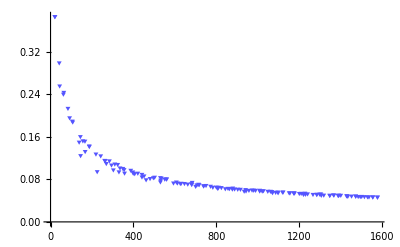
```mathematica
interlenChart2= -Graphics-;
```

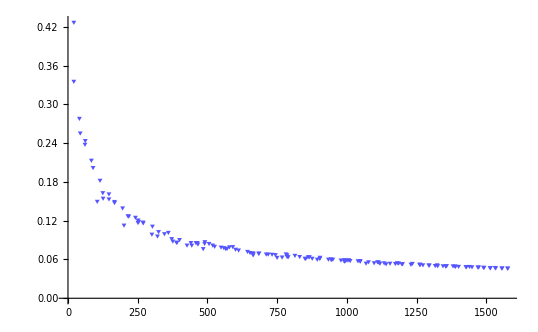
```mathematica
interlenChart1= -Graphics-;
```

```mathematica
(* delta between the middle of the interval vs delta between prediction and GT *) 

interErrvsErrChart = With[{monWin=10}, With[{infoIntPointList = tallyInfoInTriplesets[generateSuccessOutcomeWithTripleset[pairingPredMonFNR,fullTripleListNoRedun, {4,5,6,7}, (*monwin size*)monWin, (* attempts per each subset size *)2, interWald, 0.95, oneIntervalTestRetPair], "h1count",monFilenames, (*monwin again*)monWin]}, 
With[{interChart =  ListPlot[{#[[1]], (*delta between the middle of the interval and GT*)Abs[(Max@#[[2,1]]+Min@#[[2,1]])/2  - predFNR[0.1, monWin]]}&/@infoIntPointList, PlotRange->Full,PlotStyle->{Darker@Blue}, PlotMarkers->▲],  
estChart = ListPlot[{#[[1]],(*delta between prediction and gt*)Abs[#[[2,2]] - predFNR[0.1, monWin]] }&/@infoIntPointList, PlotStyle->{Darker@Magenta, PointSize[Medium]}], gtChart = chartHorLine[predFNR[0.1, monWin]]},
Show[interChart, estChart ]]]]
```

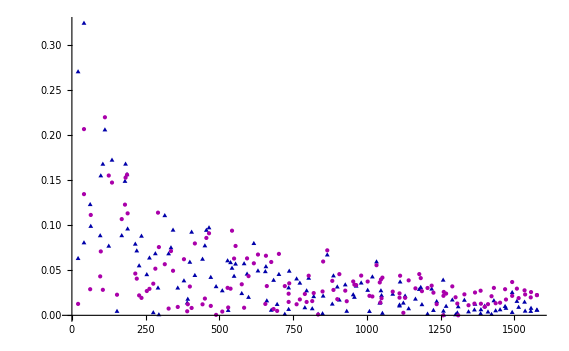
```mathematica
interErrvsErrChart1= -Graphics-;
```

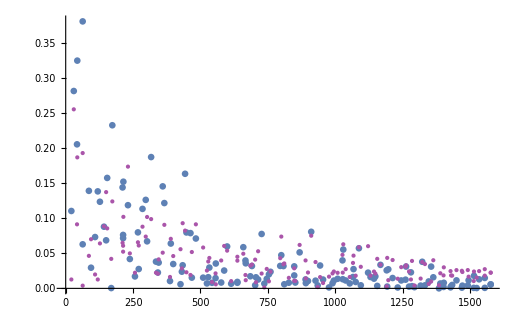

```mathematica
(*data economy: until how many samples the data is less accurate than the prediction? *) 

(* data economy eval: until when the distance is equally likely to be more?*)
With[{monWin=10}, With[{infoIntPointList = tallyInfoInTriplesets[generateSuccessOutcomeWithTripleset[pairingPredMonFNR,fullTripleListNoRedun, {4,5,6,7}, (*monwin size*)monWin, (* attempts per each subset size *)2, interWald, 0.95, oneIntervalTestRetPair], "h1count",monFilenames, monWin]}, {#[[1]], (*delta between the middle of the interval and GT*)If[Abs[(Max@#[[2,1]]+Min@#[[2,1]])/2  - predFNR[0.1, monWin]]< (*delta between prediction and gt*)Abs[#[[2,2]] - predFNR[0.1, monWin]], 1, 0]}&/@infoIntPointList]]
```

```mathematica
data ={{21,0},{21,1},{42,1},{41,0},{65,1},{65,0},{83,1},{86,1},{104,0},{106,0},{126,0},{127,0},{169,1},{152,1},{182,0},{176,1},{193,0},{189,0},{212,1},{223,1},{233,1},{236,1},{252,0},{261,0},{274,0},{273,0},{301,0},{295,1},{320,1},{318,0},{335,1},{345,0},{354,1},{371,0},{393,0},{402,0},{417,0},{407,1},{451,1},{423,1},{463,1},{459,1},{479,0},{462,0},{495,0},{488,1},{523,1},{517,0},{537,0},{541,1},{549,0},{566,0},{577,1},{596,0},{597,0},{609,1},{608,1},{631,1},{632,1},{647,1},{662,1},{656,0},{709,0},{702,1},{712,0},{718,0},{736,0},{739,0},{771,0},{742,1},{770,0},{767,1},{782,1},{805,0},{837,0},{830,0},{845,0},{828,1},{870,1},{845,0},{895,0},{893,1},{909,0},{911,1},{940,0},{942,1},{937,1},{932,0},{959,0},{960,1},{991,1},{980,1},{1014,1},{995,1},{1035,1},{1032,1},{1053,0},{1064,0},{1071,1},{1060,1},{1103,1},{1103,0},{1126,1},{1140,0},{1155,1},{1156,1},{1168,1},{1169,0},{1190,0},{1174,0},{1203,1},{1220,1},{1212,0},{1240,0},{1255,1},{1263,0},{1279,1},{1275,1},{1295,1},{1289,1},{1326,1},{1325,1},{1341,1},{1345,1},{1360,1},{1353,1},{1390,0},{1390,1},{1394,1},{1409,1},{1416,1},{1429,1},{1453,1},{1448,1},{1470,1},{1472,1},{1488,1},{1488,1},{1515,1},{1503,1},{1536,1},{1534,1},{1556,1},{1557,1},{1577,1},{1577,1}};
```

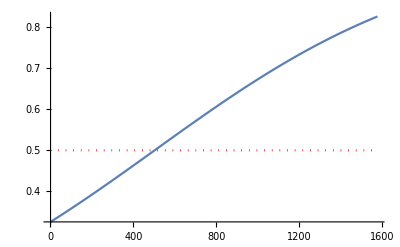

```mathematica
With[{logitmdl =LogitModelFit[data, x, x]},Show[Plot[logitmdl[x],{x, 1, Max@data[[All, 1]] }], chartHorLine[0.5, Max@data[[All, 1]],Red]]]
```

```mathematica
(** Option 1a, for random size sampling, WILSON: 
INVALID DUE TO DEPENDENCIES  **)
(* 1000 samples, random, wilson *) 
ListPlot[generatePredvsCIOutcomes[1000], PlotStyle->PointSize[Large]]
```

```mathematica
(* 10k samples, random, wilson *) 
randomOutcomes10000= generatePredvsCIOutcomes[10000]
```

{{3,0.50.40.4},{4,0.570.320.27},{5,0.890.320.09},{6,0.690.120.10},{7,0.700.090.07},{8,0.760.050.04},{9,0.7640.040.032},{10,0.7630.0270.025},{11,0.7870.0230.021},{12,0.8110.0200.019},{13,0.8130.0210.019},{14,0.8160.0220.020},{15,0.8390.0240.022},{16,0.8270.0330.029},{17,0.8510.040.034},{18,0.880.060.04},{19,0.850.130.07},{20,0.800.310.14},{21,1.000000000000000000.40.00000000000000022}}

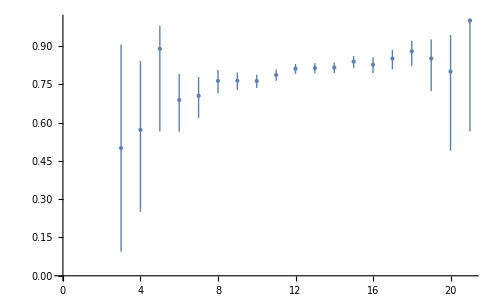

```mathematica
ListPlot[randomOutcomes10000, PlotStyle->PointSize[Large]]
```

```mathematica
(* 100k samples, random, wilson *) 
randomOutcomesWilson100000= generateMonFNRPredvsCIOutcomesWilson[100000]
```

{{3,0.570.320.27},{4,0.680.150.12},{5,0.710.070.06},{6,0.7470.040.035},{7,0.7300.0230.022},{8,0.7650.0150.014},{9,0.7740.0110.010},{10,0.7820.0080.008},{11,0.7920.0070.007},{12,0.7990.0060.006},{13,0.8070.0060.006},{14,0.8200.0070.006},{15,0.8370.0070.007},{16,0.8510.0090.009},{17,0.8570.0120.011},{18,0.8680.0190.017},{19,0.8720.0310.026},{20,0.910.050.04},{21,0.880.130.07},{22,1.000000000000000000.320.00000000000000022},{23,1.000000000000000000.60.00000000000000022}}

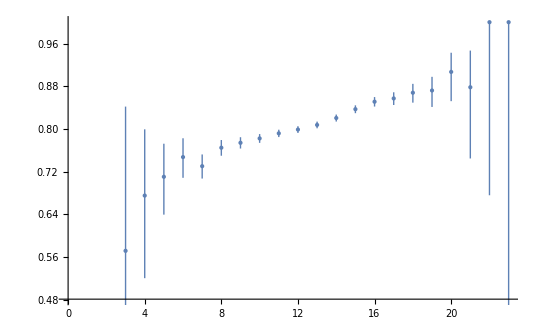

```mathematica
ListPlot[randomOutcomesWilson100000, PlotStyle->PointSize[Large]]
```

```mathematica
(* 100k samples, random,  WALD *) 
generateMonFNRPredvsCIOutcomesWald[100000]
```

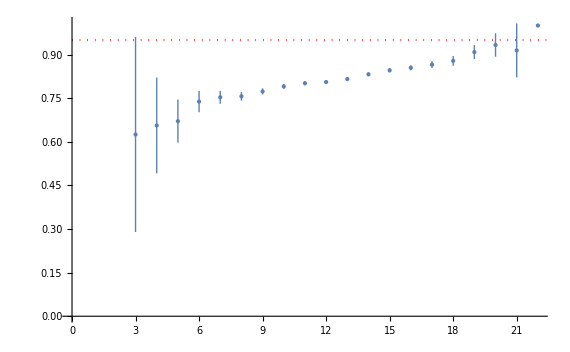

```mathematica
randomOutcomesWald100000 = ;
Show[ListPlot[randomOutcomesWald100000, PlotStyle->PointSize[Medium]], chart95conf]
```

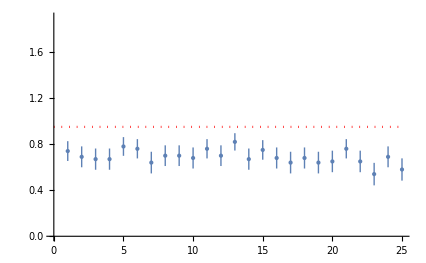
```mathematica
(*** Option 2, MONITOR FNR WITH REPLACEMENT ***) 

monfnr100sampleChartData= {{1,0.740.090.09},{2,0.690.090.09},{3,0.670.090.09},{4,0.670.090.09},{5,0.780.080.08},{6,0.760.080.08},{7,0.640.090.09},{8,0.700.090.09},{9,0.700.090.09},{10,0.680.090.09},{11,0.760.080.08},{12,0.700.090.09},{13,0.820.080.08},{14,0.670.090.09},{15,0.750.080.08},{16,0.680.090.09},{17,0.640.090.09},{18,0.680.090.09},{19,0.640.090.09},{20,0.650.090.09},{21,0.760.080.08},{22,0.650.090.09},{23,0.540.100.10},{24,0.690.090.09},{25,0.580.100.10}};
Show[chart95conf[25],ListPlot[monfnr100sampleChartData, PlotStyle->PointSize[Medium]]]
-Graphics-
```

```mathematica
(** Option 4, THREE-WAY VISUALS FOR WILSON **) 

(* 100 samples per subset, that's not enough data *) 
generateCIOutcomesPerSubsetSize[triplingMonFNRCIPredGt, 100, interWilson, interWilson, oneIntervalTripleTest]
```

```mathematica
threewayPerSubset100 = ;
```

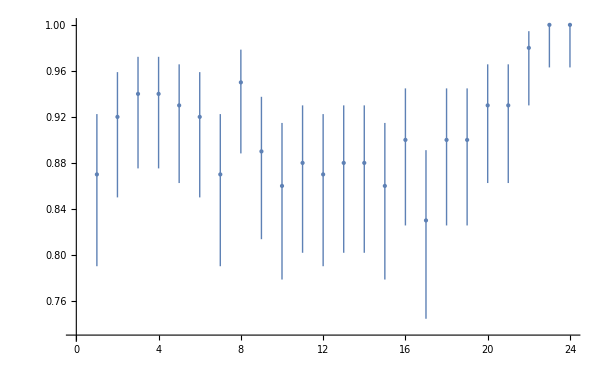

```mathematica
ListPlot[threewayPerSubset100, PlotStyle->PointSize[Large]]
```

```mathematica
(* 1k samples per subset *) 
generateCIOutcomesPerSubsetSize[triplingMonFNRCIPredGt, 1000, interWilson, interWilson, oneIntervalTripleTest]
```

```mathematica
threewayPerSubset1000 = ;
```

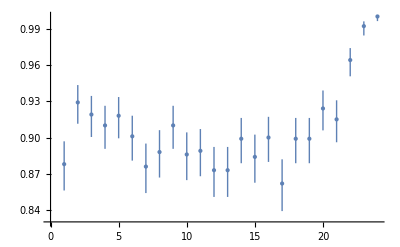

```mathematica
ListPlot[threewayPerSubset1000, PlotStyle->PointSize[Large]]
```

```mathematica
(* 10k samples per subset *)
generateCIOutcomesPerSubsetSize[triplingMonFNRCIPredGt, 10000, interWilson, interWilson, oneIntervalTripleTest]
```

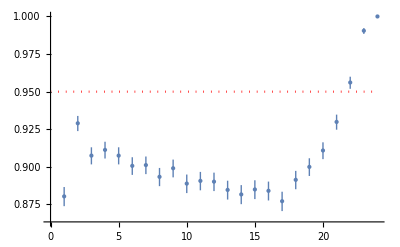

```mathematica
threewayPerSubset10000Wilson = ;
Show[ListPlot[threewayPerSubset10000Wilson, PlotStyle->PointSize[Medium]], chart95conf]
```

```mathematica
(* Option 4, THREE-WAY VISUALS FOR WALD *) 

generateCIOutcomesPerSubsetSize[triplingMonFNRCIPredGt, 1000, interWald, interWald, oneIntervalTripleTest]
```

```mathematica
threewayPerSubset1000Wald = ;
```

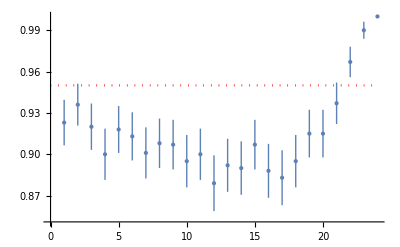

```mathematica
Show[ListPlot[threewayPerSubset1000Wald, PlotStyle->PointSize[Large]], chart95conf]
```

```mathematica
generateCIOutcomesPerSubsetSize[triplingMonFNRCIPredGt, 10000, interWald, interWald, oneIntervalTripleTest]
```

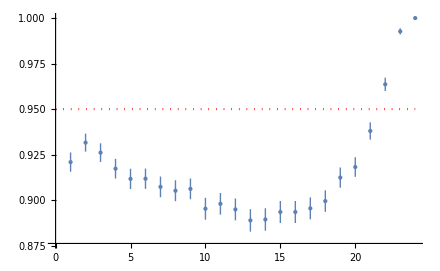

```mathematica
threewayPerSubset10000Wald = ;
(* depressing slope, weird *) 
Show[ListPlot[threewayPerSubset10000Wald, PlotStyle->PointSize[Medium]], chart95conf]
```

```mathematica
(* three sessions 4-6, with redundancy *) 
generateCIOutcomesPerSubsetSize[threewayPairingMonFNRCIPredGt,fullTripleList,{4,5,6},10,1000,interWald,interWald,0.95,oneIntervalThreewayTest]
```

```mathematica
threewayPerSubset10000WaldFull= {{1,0.9060.0180.018},{2,0.8980.0190.019},{3,0.8790.0200.020},{4,0.8910.0190.019},{5,0.9070.0180.018},{6,0.8940.0190.019},{7,0.8940.0190.019},{8,0.9030.0180.018},{9,0.8970.0190.019},{10,0.8890.0190.019},{11,0.9150.0170.017},{12,0.8950.0190.019},{13,0.9050.0180.018},{14,0.9120.0180.018},{15,0.9060.0180.018},{16,0.9000.0190.019},{17,0.8980.0190.019},{18,0.9080.0180.018},{19,0.9240.0160.016},{20,0.9080.0180.018},{21,0.8940.0190.019},{22,0.9060.0180.018},{23,0.9110.0180.018},{24,0.9210.0170.017},{25,0.9130.0170.017},{26,0.9270.0160.016},{27,0.9020.0180.018},{28,0.9070.0180.018},{29,0.9300.0160.016},{30,0.9130.0170.017},{31,0.9200.0170.017},{32,0.9140.0170.017},{33,0.9160.0170.017},{34,0.9390.0150.015},{35,0.9190.0170.017},{36,0.9320.0160.016},{37,0.9270.0160.016},{38,0.9410.0150.015},{39,0.9140.0170.017},{40,0.9190.0170.017},{41,0.9260.0160.016},{42,0.9350.0150.015},{43,0.9280.0160.016},{44,0.9400.0150.015},{45,0.9530.0130.013},{46,0.9480.0140.014},{47,0.9490.0140.014},{48,0.9480.0140.014},{49,0.9470.0140.014},{50,0.9550.0130.013},{51,0.9660.0110.011},{52,0.9690.0110.011},{53,0.9730.0100.010},{54,1.000000000000000001122}};
```

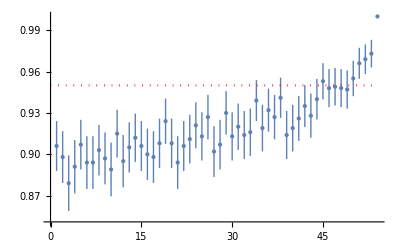

```mathematica
Show[ListPlot[threewayPerSubset10000WaldFull, PlotStyle->PointSize[Medium]], chart95conf[54]]
```

```mathematica
(* three sessions 4-6, without redundancy *) 
generateCIOutcomesPerSubsetSize[threewayPairingMonFNRCIPredGt,fullTripleListNoRedun,{4,5,6},10,1000,interWald,interWald,0.95,oneIntervalThreewayTest]
```

```mathematica
threewayPerSubset10000WaldNoRedun= {{1,0.8840.0200.020},{2,0.8710.0210.021},{3,0.8770.0200.020},{4,0.8660.0210.021},{5,0.8570.0220.022},{6,0.8650.0210.021},{7,0.8430.0230.023},{8,0.8390.0230.023},{9,0.8540.0220.022},{10,0.8640.0210.021},{11,0.8570.0220.022},{12,0.8550.0220.022},{13,0.8810.0200.020},{14,0.8760.0200.020},{15,0.8660.0210.021},{16,0.8650.0210.021},{17,0.8670.0210.021},{18,0.8810.0200.020},{19,0.8730.0210.021},{20,0.8670.0210.021},{21,0.8750.0200.020},{22,0.8730.0210.021},{23,0.8610.0210.021},{24,0.8490.0220.022},{25,0.8770.0200.020},{26,0.8520.0220.022},{27,0.8550.0220.022},{28,0.8860.0200.020},{29,0.8760.0200.020},{30,0.8620.0210.021},{31,0.9070.0180.018},{32,0.9160.0170.017},{33,0.9390.0150.015},{34,1.000000000000000001122}};
```

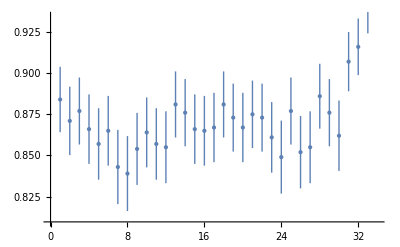

```mathematica
Show[ListPlot[threewayPerSubset10000WaldNoRedun, PlotStyle->PointSize[Medium]], chart95conf[34]]
```

```mathematica
(*** GROUND TRUTHS: TESTING WILSON CI FOR MONITOR FNR: data-driven Wilson CI for monitor FNR vs FNR ground truth ***) 
(* an outcome whether GT is in CI interval described by pairlist *) 

oneIntervalGtTestWilson[pairIdList_] := IntervalMemberQ[(* interval *) interWilson[countFromFiles[ "FNcount",monFilenames[10, pairIdList]], countFromFiles[ "h1count",monFilenames[10, pairIdList]], 0.95], (* prediction *) predFNR[0.1, 10]];

(* a pair of interval (described by pairlist) and GT *)
oneIntervalGtTestPairWilson[pairIdList_] := {(* interval *) interWilson[countFromFiles[ "FNcount",monFilenames[10, pairIdList]], countFromFiles[ "h1count",monFilenames[10, pairIdList]], 0.95], (* prediction *)  predFNR[0.1, 10]};
```

```mathematica
(* fixed subsets CI vs mon FNR GT *) 
generateGtSuccessCountsPerSubsetSizeWilson:= With[{subsetsCt = #},
(* count truths *)Count[oneIntervalGtTestWilson[#]&/@ (* all possible sets of pairs for tests *) Subsets[Flatten[Outer[List, Range[1,5], Range[1,5]], 1], {subsetsCt},{#}] &/@ (* getting random 100 subsets *)  RandomInteger[{1,(*counting subsets *)Length@Subsets[Flatten[Outer[List, Range[1,5], Range[1,5]], 1], {subsetsCt}]
},100], {True}]
]& /@ Range[1, 24];
```

```mathematica
(* 100 runs of 100 samples each *) 
Table[generateGtSuccessCountsPerSubsetSizeWilson, 100]
```

```mathematica
resGtLists100Wilson =
```

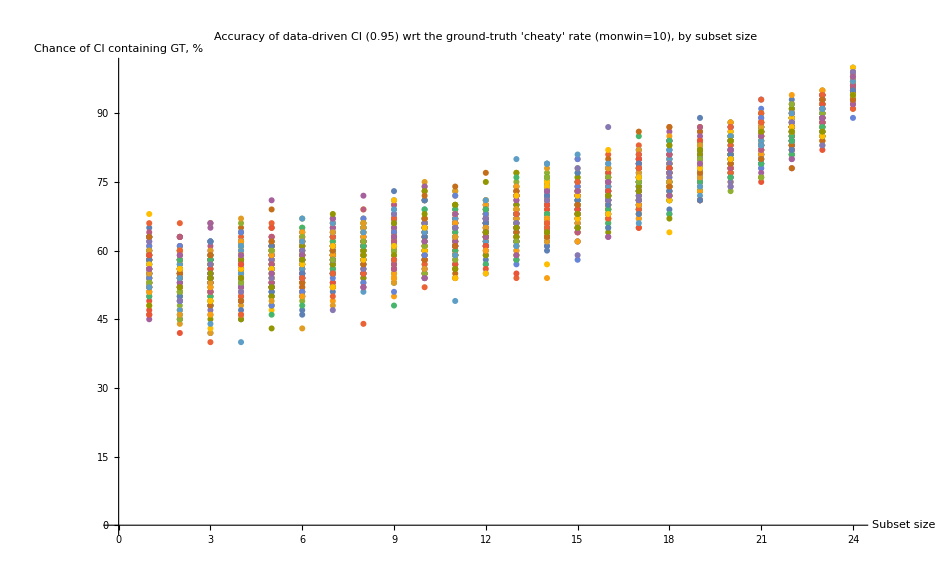

```mathematica
ListPlot[Inner[List, Range[1,24], #, List]& /@ resGtLists100Wilson, AxesLabel->{"Subset size", "Chance of CI containing GT, %"}, PlotLabel->"Accuracy of data-driven CI (0.95) wrt the ground-truth 'cheaty' rate (monwin=10), by subset size"]
```

```mathematica
(*** TESTING WALD CI FOR MONITOR FNR GT ***)
```

```mathematica
(* an outcome whether GT is in CI interval described by pairlist *) 

oneIntervalGtTestWald[pairIdList_] := IntervalMemberQ[(* interval *) interWald[countFromFiles[ "FNcount",monFilenames[10, pairIdList]], countFromFiles[ "h1count",monFilenames[10, pairIdList]], 0.95], (* prediction *) predFNR[0.1, 10]];

(* a pair of interval (described by pairlist) and GT *)
oneIntervalGtTestPairWald[pairIdList_] := {(* interval *) interWald[countFromFiles[ "FNcount",monFilenames[10, pairIdList]], countFromFiles[ "h1count",monFilenames[10, pairIdList]], 0.95], (* prediction *)  predFNR[0.1, 10]};
```

```mathematica
generateGtSuccessCountsPerSubsetSizeWald:= With[{subsetsCt = #},
(* count truths *)Count[oneIntervalGtTestWald[#]&/@ (* all possible sets of pairs for tests *) Subsets[Flatten[Outer[List, Range[1,5], Range[1,5]], 1], {subsetsCt},{#}] &/@ (* getting random 100 subsets *)  RandomInteger[{1,(*counting subsets *)Length@Subsets[Flatten[Outer[List, Range[1,5], Range[1,5]], 1], {subsetsCt}]
},100], {True}]
]& /@ Range[1, 24];
```

```mathematica
(* Option 1b GT, 100 runs of 100 samples each *) 
Table[generateGtSuccessCountsPerSubsetSizeWald, 100]
```

```mathematica
resListsWald100 = ;
```

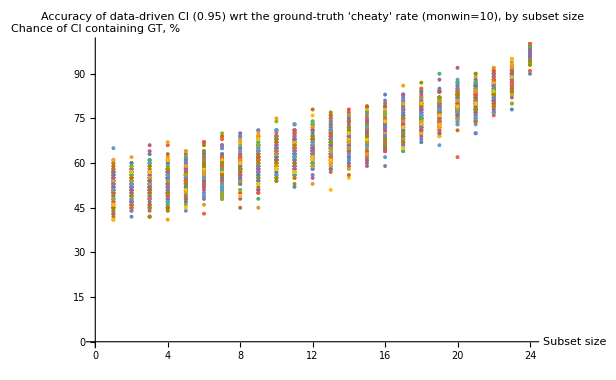

```mathematica
ListPlot[Inner[List, Range[1,24], #, List]& /@ resListsWald100a, AxesLabel->{"Subset size", "Chance of CI containing GT, %"}, PlotLabel->"Accuracy of data-driven CI (0.95) wrt the ground-truth 'cheaty' rate (monwin=10), by subset size"]
```

```mathematica
ListPlot[Inner[List, Range[1,24], #, List]& /@ resListsWald100b, AxesLabel->{"Subset size", "Chance of CI containing GT, %"}, PlotLabel->"Accuracy of data-driven CI (0.95) wrt the ground-truth 'cheaty' rate (monwin=10), by subset size"]
```

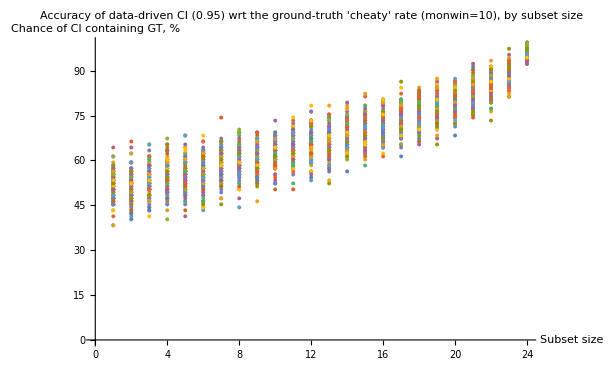

```mathematica
(* on sessions 4-6, GT *) 
generateCIOutcomesPerSubsetSize[pairingGtMonFNR,fullTripleListNoRedun, {4,5,6}, (*monwin size*) 10, (* attempts per subset size *)1000]
```

```mathematica
resGtMonFnr1000={{1,0.5430.0310.031},{2,0.4520.0310.031},{3,0.5000.0310.031},{4,0.4890.0310.031},{5,0.5040.0310.031},{6,0.5200.0310.031},{7,0.5430.0310.031},{8,0.5740.0310.031},{9,0.5750.0310.031},{10,0.5950.0300.030},{11,0.5600.0310.031},{12,0.5740.0310.031},{13,0.6090.0300.030},{14,0.5920.0300.030},{15,0.6120.0300.030},{16,0.6320.0300.030},{17,0.6570.0290.029},{18,0.6610.0290.029},{19,0.6780.0290.029},{20,0.6900.0290.029},{21,0.7080.0280.028},{22,0.7010.0280.028},{23,0.7400.0270.027},{24,0.7560.0270.027},{25,0.7690.0260.026},{26,0.7810.0260.026},{27,0.8230.0240.024},{28,0.8150.0240.024},{29,0.8650.0210.021},{30,0.8970.0190.019},{31,0.9210.0170.017},{32,0.9530.0130.013},{33,1.000000000000000001122},{34,1.000000000000000001122}};
```

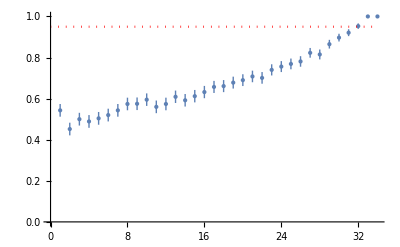

```mathematica
Show[ListPlot[resGtMonFnr1000, PlotStyle->PointSize[Medium]], chart95conf[34]]
```

```mathematica
(* same as above but with session 7 *) 
generateCIOutcomesPerSubsetSize[pairingGtMonFNR,fullTripleListNoRedun, {4,5,6,7}, (*monwin size*) 10, (* attempts per subset size *)1000]
```

```mathematica
resGtMonFnr1000={{1,0.4620.0310.031},{2,0.4280.0310.031},{3,0.4720.0310.031},{4,0.4630.0310.031},{5,0.4820.0310.031},{6,0.4900.0310.031},{7,0.5240.0310.031},{8,0.5060.0310.031},{9,0.5230.0310.031},{10,0.5190.0310.031},{11,0.5110.0310.031},{12,0.5060.0310.031},{13,0.5110.0310.031},{14,0.5510.0310.031},{15,0.5310.0310.031},{16,0.5330.0310.031},{17,0.5590.0310.031},{18,0.5790.0310.031},{19,0.5750.0310.031},{20,0.6010.0300.030},{21,0.5730.0310.031},{22,0.5790.0310.031},{23,0.6120.0300.030},{24,0.6090.0300.030},{25,0.5800.0310.031},{26,0.6020.0300.030},{27,0.6050.0300.030},{28,0.6020.0300.030},{29,0.6150.0300.030},{30,0.6250.0300.030},{31,0.6180.0300.030},{32,0.6370.0300.030},{33,0.6540.0290.029},{34,0.6470.0300.030},{35,0.6430.0300.030},{36,0.6420.0300.030},{37,0.6790.0290.029},{38,0.6730.0290.029},{39,0.6630.0290.029},{40,0.6720.0290.029},{41,0.6900.0290.029},{42,0.7200.0280.028},{43,0.6990.0280.028},{44,0.6860.0290.029},{45,0.7210.0280.028},{46,0.7140.0280.028},{47,0.7540.0270.027},{48,0.7490.0270.027},{49,0.7460.0270.027},{50,0.7650.0260.026},{51,0.7590.0270.027},{52,0.7740.0260.026},{53,0.7870.0250.025},{54,0.7900.0250.025},{55,0.8130.0240.024},{56,0.8150.0240.024},{57,0.8590.0220.022},{58,0.8640.0210.021},{59,0.8690.0210.021},{60,0.8570.0220.022},{61,0.8820.0200.020},{62,0.9170.0170.017},{63,0.9100.0180.018},{64,0.9330.0150.015},{65,0.9350.0150.015},{66,0.9630.0120.012},{67,0.9510.0130.013},{68,0.9780.0090.009},{69,0.9870.0070.007},{70,0.9900.0060.006},{71,0.99800.00280.0028},{72,1.000000000000000001122},{73,1.000000000000000001122}};
```

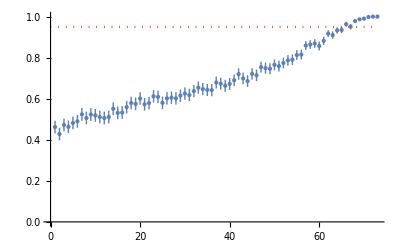

```mathematica
Show[ListPlot[resGtMonFnr1000, PlotStyle->PointSize[Medium]], chart95conf[73]]
```

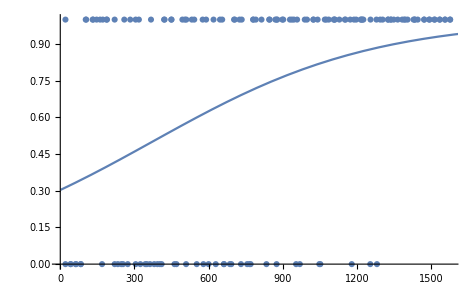
```mathematica
(* drawing the logit based on information amount *) 
Show[%377,Plot[logit376[x],{x, 1, 3000}]]
-Graphics-
(** Option 1a GT, randomized sampling for wald CI vs ground truth monitor FNR **)
```

```mathematica
(* a list of pairs {subset size, whether CI contains the prediciton} *) 
generateMonGtFNRvsCISample[sampleCt_]:= ({#[[1]],oneIntervalGtTestWald[#[[2]]]}&/@( Flatten[{Length@#, #} &/@(* list of lists of subsets possible sets of pairs for tests *) Subsets[Flatten[Outer[List, Range[1,5], Range[1,5]], 1], {1,25},{#}] &/@ (* getting random 100 subsets *)  RandomInteger[{1,(*all subsets *)subsetCt
},sampleCt],1]));


(* converting tallied triples to ratios and stdev, getting pairs {subset size, accuracy w/uncert based on wilson CIs} *) 
generateMonGtFNRvsCIOutcomesWald[sampleCt_]:={(*subset size*) #[[1]], (*ratio of successes to total *) With[{est = #[[2]]/(#[[2]]+#[[3]]), int = interWald[#[[2]],#[[2]]+#[[3]], 0.95]},Around[(*estimated accuracy*)est,(* converting wilson interval to uncertainty bounds*) {Min@int-est, Max@int-est}]] }&/@ (* getting tallied sample data and filtering it*)Select[tallyUpPredvsCISample[generateMonGtFNRvsCISample[sampleCt]], #[[2]] >0 ∨ #[[3]]>0 # &];
```

```mathematica
(* 10k samples randomly *)
generateMonGtFNRvsCIOutcomesWald[10000]
```

```mathematica
randomOutcomesMonFNRGtWald10000 = {{5,0.450.220.22},{6,0.400.130.13},{7,0.550.080.08},{8,0.590.050.05},{9,0.570.040.04},{10,0.6010.0300.030},{11,0.6260.0270.027},{12,0.6360.0240.024},{13,0.6760.0230.023},{14,0.6820.0250.025},{15,0.6960.0290.029},{16,0.7360.0350.035},{17,0.780.040.04},{18,0.730.080.08},{19,0.800.110.11},{20,1.000000000000000001122},{21,0.70.50.5}};
```

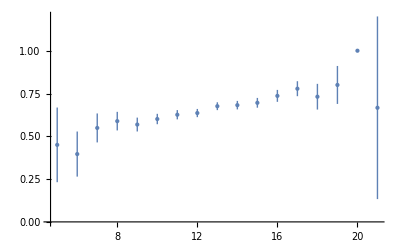

```mathematica
ListPlot[randomOutcomesMonFNRGtWald10000, PlotStyle->PointSize[Large]]
```

```mathematica
(* 100k samples randomly *) 
generateMonGtFNRvsCIOutcomesWald[100000]
```

```mathematica
randomOutcomesMonFNRGtWald100000 ={{3,0.200.200.35},{4,0.440.160.16},{5,0.480.080.08},{6,0.580.040.04},{7,0.5830.0250.025},{8,0.5970.0170.017},{9,0.5960.0120.012},{10,0.6150.0100.010},{11,0.6330.0080.008},{12,0.6500.0070.007},{13,0.6680.0070.007},{14,0.6810.0080.008},{15,0.6980.0090.009},{16,0.7170.0110.011},{17,0.7470.0150.015},{18,0.7740.0210.021},{19,0.760.040.04},{20,0.800.060.06},{21,0.870.100.10},{22,1.000000000000000001122},{23,1.000000000000000001122}};
```

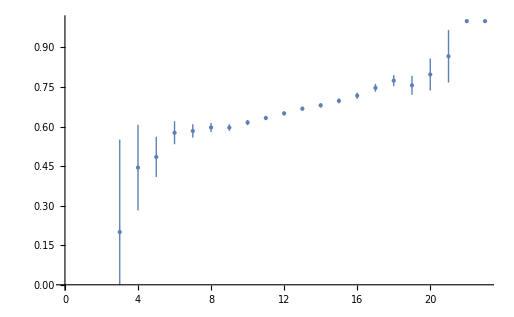

```mathematica
ListPlot[randomOutcomesMonFNRGtWald100000, PlotStyle->PointSize[Large]]
```

```mathematica
(** NICE PRESENTATION-READY COMBINATIONS OF THE ABOVE **)
```

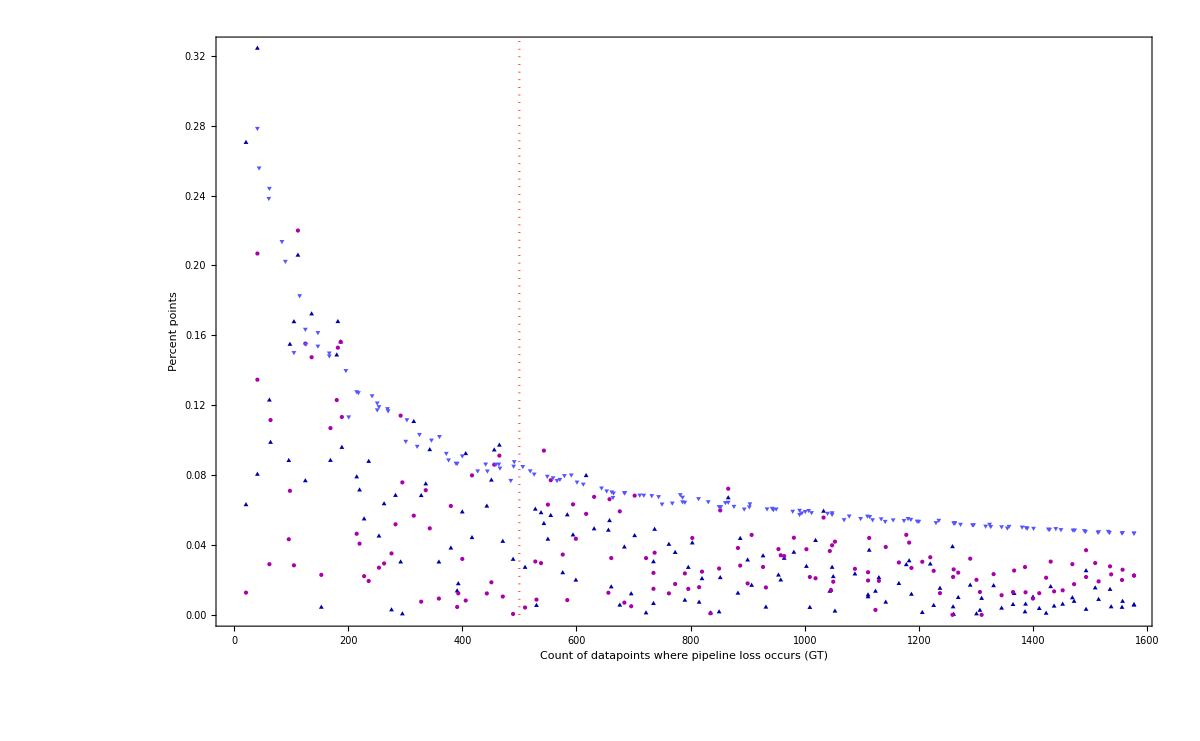

```mathematica
Show[interErrvsErrChart1, interlenChart1, chartVertLine[500,1,0,Red],Frame->True, FrameLabel->{Style["Count of datapoints where pipeline loss occurs (GT)", 14],Style["Percent points", 14]},   ImageSize -> 1200]
```

```mathematica
Export["~/graph.png",%697, ImageSize->1000] ;
```

```mathematica
SwatchLegend[{ Lighter@Blue,Darker@Blue,Darker@Magenta, Red},{"Confidence interval length of data-based FNR estimates","Absolute error of the midpoint of the data-based FNR confidence interval","Absolute error of our FNR estimate","Point where the absolute errors (above) are equivalent"}, LegendMarkers->{ ▼, ▲,●,"--"}]
```

```mathematica
Export["~/graph.png",%691, ImageSize->1200] ;
```